## Updated Data

Used scraping code from “GoL-10-Data” in FromBrad

```mathematica
fixedFinalCut =;
```

```mathematica
addThese = ;
```

```mathematica
lifeData=Merge[{fixedFinalCut,addThese},First];
```

```mathematica
newLifeNames=
ReverseSortBy[
KeyTake[Append[GroupBy[Values[lifeData], (#Class&)->(#Name&)], "Reflector"-> {}],Keys[$LifeNames]], Length];
```

Conclusion, was able to get the updated data which has results from 2024 and 2025, see next section for the differences of the two dataset

## Comparing old data and new data

### Having trouble exactly recreating $LifeNames

```mathematica
newfromgol10 = ;
```

```mathematica
oldfromgol10 = ;
```

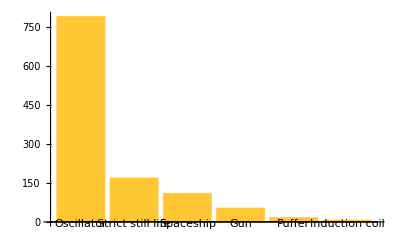

```mathematica
BarChart[ReverseSort[Length/@oldfromgol10], ChartLabels->Automatic]
```

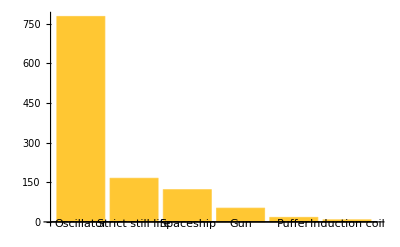

```mathematica
BarChart[ReverseSort[Length/@newfromgol10], ChartLabels->Automatic]
```

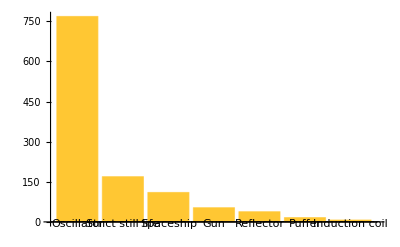

```mathematica
BarChart[ReverseSort[Length/@$LifeNames], ChartLabels->Automatic]
```

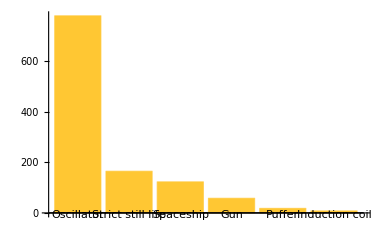

```mathematica
BarChart[ReverseSort[Length/@newLifeNames], ChartLabels->Automatic]
```

### Comparing old LifeData to new LifeData

```mathematica
diffs= Complement[$LifeData, lifeData];
```

```mathematica
differencesDetailed=Select[Flatten[Table[{name,column},{name,Keys[$LifeData]},{column,Keys[$LifeData[name]]}],1],$LifeData[#[[1]]][#[[2]]]=!=lifeData[#[[1]]][#[[2]]]&]
```

{{Traffic light,Class},{Traffic light,Period},{Cuphook,Class},{Cuphook,DataFiles},{Cuphook,MatrixData},{Heavyweight spaceship,Speed},{Lightweight spaceship,Speed},{Middleweight spaceship,Speed},{V spark,Name},{V spark,Year},{V spark,Class},{V spark,Wiki},{V spark,DataFiles},{V spark,MatrixData},{V spark,InitialWeight},{Ecologist,Speed},{Ecologist,DataFiles},{Interchange,Name},{Interchange,Year},{Interchange,Class},{Interchange,Period},{Interchange,Wiki},{Interchange,DataFiles},{Interchange,MatrixData},{Interchange,InitialWeight},{Iwona active region,Name},{Iwona active region,Year},{Iwona active region,Class},{Iwona active region,Wiki},{Iwona active region,DataFiles},{Iwona active region,MatrixData},{Iwona active region,InitialWeight},{Orthogonal on-off,Name},{Orthogonal on-off,Year},{Orthogonal on-off,Class},{Orthogonal on-off,Wiki},{Orthogonal on-off,DataFiles},{Orthogonal on-off,MatrixData},{Orthogonal on-off,InitialWeight},{1-2-3,Name},{1-2-3,Year},{1-2-3,Class},{1-2-3,Period},{1-2-3,Wiki},{1-2-3,DataFiles},{1-2-3,MatrixData},{1-2-3,InitialWeight},{Schick engine,Speed},{Snake dance,Name},{Snake dance,Year},{Snake dance,Class},{Snake dance,Period},{Snake dance,Wiki},{Snake dance,DataFiles},{Snake dance,MatrixData},{Snake dance,InitialWeight},{Snake pit,Name},{Snake pit,Year},{Snake pit,Class},{Snake pit,Period},{Snake pit,Wiki},{Snake pit,DataFiles},{Snake pit,MatrixData},{Snake pit,InitialWeight},{Snake siamese snake,Name},{Snake siamese snake,Year},{Snake siamese snake,Class},{Snake siamese snake,Wiki},{Snake siamese snake,DataFiles},{Snake siamese snake,MatrixData},{Snake siamese snake,InitialWeight},{$rats,Name},{$rats,Year},{$rats,Class},{$rats,Period},{$rats,Wiki},{$rats,DataFiles},{$rats,MatrixData},{$rats,InitialWeight},{Eater plug,Name},{Eater plug,Year},{Eater plug,Class},{Eater plug,Period},{Eater plug,Wiki},{Eater plug,DataFiles},{Eater plug,MatrixData},{Eater plug,InitialWeight},{Eater tail siamese eater tail,Name},{Eater tail siamese eater tail,Year},{Eater tail siamese eater tail,Class},{Eater tail siamese eater tail,Wiki},{Eater tail siamese eater tail,DataFiles},{Eater tail siamese eater tail,MatrixData},{Eater tail siamese eater tail,InitialWeight},{Snake bridge snake,Name},{Snake bridge snake,Year},{Snake bridge snake,Class},{Snake bridge snake,Wiki},{Snake bridge snake,DataFiles},{Snake bridge snake,MatrixData},{Snake bridge snake,InitialWeight},{Snake siamese very long snake,Name},{Snake siamese very long snake,Year},{Snake siamese very long snake,Class},{Snake siamese very long snake,Wiki},{Snake siamese very long snake,DataFiles},{Snake siamese very long snake,MatrixData},{Snake siamese very long snake,InitialWeight},{Up snake on table,Name},{Up snake on table,Year},{Up snake on table,Class},{Up snake on table,Wiki},{Up snake on table,DataFiles},{Up snake on table,MatrixData},{Up snake on table,InitialWeight},{Heavyweight emulator,DataFiles},{Lightweight emulator,DataFiles},{Middleweight emulator,DataFiles},{p10 traffic light hassler,Name},{p10 traffic light hassler,Year},{p10 traffic light hassler,Class},{p10 traffic light hassler,Period},{p10 traffic light hassler,Wiki},{p10 traffic light hassler,DataFiles},{p10 traffic light hassler,MatrixData},{p10 traffic light hassler,InitialWeight},{Jack,Name},{Jack,Year},{Jack,Class},{Jack,Period},{Jack,Wiki},{Jack,DataFiles},{Jack,MatrixData},{Jack,InitialWeight},{Jam,Name},{Jam,Year},{Jam,Class},{Jam,Period},{Jam,Wiki},{Jam,DataFiles},{Jam,MatrixData},{Jam,InitialWeight},{106P135,Name},{106P135,Year},{106P135,Class},{106P135,Period},{106P135,Wiki},{106P135,DataFiles},{106P135,MatrixData},{106P135,InitialWeight},{1-2-3-4,Name},{1-2-3-4,Year},{1-2-3-4,Class},{1-2-3-4,Period},{1-2-3-4,Wiki},{1-2-3-4,DataFiles},{1-2-3-4,MatrixData},{1-2-3-4,InitialWeight},{10-engine Cordership,Name},{10-engine Cordership,Year},{10-engine Cordership,Class},{10-engine Cordership,Period},{10-engine Cordership,Speed},{10-engine Cordership,Wiki},{10-engine Cordership,DataFiles},{10-engine Cordership,MatrixData},{10-engine Cordership,InitialWeight},{13-engine Cordership,Speed},{Caber tosser 1,Name},{Caber tosser 1,Year},{Caber tosser 1,Class},{Caber tosser 1,Wiki},{Caber tosser 1,DataFiles},{Caber tosser 1,MatrixData},{Caber tosser 1,InitialWeight},{117P9H3V0,Name},{117P9H3V0,Year},{117P9H3V0,Class},{117P9H3V0,Period},{117P9H3V0,Speed},{117P9H3V0,Wiki},{117P9H3V0,DataFiles},{117P9H3V0,MatrixData},{117P9H3V0,InitialWeight},{Hivenudger,Speed},{Hivenudger,DataFiles},{Pushalong 1,Speed},{Sidecar,Speed},{x66,Speed},{7-engine Cordership,Speed},{Glider pusher,Class},{101,Name},{101,Year},{101,Class},{101,Period},{101,Wiki},{101,DataFiles},{101,MatrixData},{101,InitialWeight},{Three-block shifter,Class},{Coe ship,Speed},{Period-184 glider gun,Wiki},{Period-246 glider gun,Wiki},{p15 pre-pulsar spaceship,Speed},{p6 pipsquirter,DataFiles},{Period-24 glider gun,Name},{Period-24 glider gun,Year},{Period-24 glider gun,Class},{Period-24 glider gun,Period},{Period-24 glider gun,Wiki},{Period-24 glider gun,DataFiles},{Period-24 glider gun,MatrixData},{Period-24 glider gun,InitialWeight},{6-engine Cordership,Speed},{7-in-a-row Cordership,Speed},{8-engine Cordership,Speed},{Callahan G-to-H,Name},{Callahan G-to-H,Year},{Callahan G-to-H,Class},{Callahan G-to-H,Wiki},{Callahan G-to-H,DataFiles},{Callahan G-to-H,MatrixData},{Callahan G-to-H,InitialWeight},{p5 bouncer,Class},{p6 bouncer,Class},{p7 bouncer,Class},{p8 bouncer,Class},{Pre-pulsar spaceship,Speed},{Silver's reflector,Class},{Orion 2,Name},{Orion 2,Year},{Orion 2,Class},{Orion 2,Period},{Orion 2,Speed},{Orion 2,Wiki},{Orion 2,DataFiles},{Orion 2,MatrixData},{Orion 2,InitialWeight},{p49 bouncer loop,DataFiles},{p49 bouncer loop,MatrixData},{p49 bouncer loop,InitialWeight},{p7 pipsquirter,DataFiles},{72P6H2V0,Speed},{Period-22 glider gun,Name},{Period-22 glider gun,Year},{Period-22 glider gun,Class},{Period-22 glider gun,Period},{Period-22 glider gun,Wiki},{Period-22 glider gun,DataFiles},{Period-22 glider gun,MatrixData},{Period-22 glider gun,InitialWeight},{55P9H3V0,Speed},{Boojum reflector,Class},{31P8H4V0,Speed},{p15 bouncer,Class},{(13,1)c/31 Pseudo-B climber,Name},{(13,1)c/31 Pseudo-B climber,Year},{(13,1)c/31 Pseudo-B climber,Class},{(13,1)c/31 Pseudo-B climber,Speed},{(13,1)c/31 Pseudo-B climber,Wiki},{(13,1)c/31 Pseudo-B climber,DataFiles},{(13,1)c/31 Pseudo-B climber,MatrixData},{(13,1)c/31 Pseudo-B climber,InitialWeight},{Jason's p11,Name},{Jason's p11,Year},{Jason's p11,Class},{Jason's p11,Period},{Jason's p11,Wiki},{Jason's p11,DataFiles},{Jason's p11,MatrixData},{Jason's p11,InitialWeight},{V gun,Name},{V gun,Year},{V gun,Class},{V gun,Period},{V gun,Wiki},{V gun,DataFiles},{V gun,MatrixData},{V gun,InitialWeight},{160P10H2V0,Speed},{3-engine Cordership,Speed},{Iwona,Name},{Iwona,Year},{Iwona,Class},{Iwona,Wiki},{Iwona,DataFiles},{Iwona,MatrixData},{Iwona,InitialWeight},{4-engine Cordership,Speed},{5-engine Cordership,Speed},{(23,5)c/79 Herschel climber,Name},{(23,5)c/79 Herschel climber,Year},{(23,5)c/79 Herschel climber,Class},{(23,5)c/79 Herschel climber,Speed},{(23,5)c/79 Herschel climber,Wiki},{(23,5)c/79 Herschel climber,DataFiles},{(23,5)c/79 Herschel climber,MatrixData},{(23,5)c/79 Herschel climber,InitialWeight},{OTCA metapixel,Name},{OTCA metapixel,Year},{OTCA metapixel,Class},{OTCA metapixel,Wiki},{OTCA metapixel,DataFiles},{OTCA metapixel,MatrixData},{OTCA metapixel,InitialWeight},{Ship+fishhook,Class},{Sidewinder,Speed},{Sidewinder,DataFiles},{p1 megacell,Name},{p1 megacell,Year},{p1 megacell,Class},{p1 megacell,Wiki},{p1 megacell,DataFiles},{p1 megacell,MatrixData},{p1 megacell,InitialWeight},{44P12.3,Name},{44P12.3,Year},{44P12.3,Class},{44P12.3,Period},{44P12.3,Wiki},{44P12.3,DataFiles},{44P12.3,MatrixData},{44P12.3,InitialWeight},{487-tick reflector,Class},{Rectifier,Class},{110P62,Name},{110P62,Year},{110P62,Class},{110P62,Period},{110P62,Wiki},{110P62,DataFiles},{110P62,MatrixData},{110P62,InitialWeight},{6-in-a-row Cordership,Speed},{74P8H2V0,Speed},{c/5 diagonal rake,Name},{c/5 diagonal rake,Year},{c/5 diagonal rake,Class},{c/5 diagonal rake,Period},{c/5 diagonal rake,Speed},{c/5 diagonal rake,Wiki},{c/5 diagonal rake,DataFiles},{c/5 diagonal rake,MatrixData},{c/5 diagonal rake,InitialWeight},{p44 traffic light hassler,Name},{p44 traffic light hassler,Year},{p44 traffic light hassler,Class},{p44 traffic light hassler,Period},{p44 traffic light hassler,Wiki},{p44 traffic light hassler,DataFiles},{p44 traffic light hassler,MatrixData},{p44 traffic light hassler,InitialWeight},{86P6H3V0,Speed},{p4 reflector,Class},{(34,7)c/156 Herschel climber,Name},{(34,7)c/156 Herschel climber,Year},{(34,7)c/156 Herschel climber,Class},{(34,7)c/156 Herschel climber,Speed},{(34,7)c/156 Herschel climber,Wiki},{(34,7)c/156 Herschel climber,DataFiles},{(34,7)c/156 Herschel climber,MatrixData},{(34,7)c/156 Herschel climber,InitialWeight},{CC semi-Snark,Class},{Period-20 glider gun,Name},{Period-20 glider gun,Year},{Period-20 glider gun,Class},{Period-20 glider gun,Period},{Period-20 glider gun,Wiki},{Period-20 glider gun,DataFiles},{Period-20 glider gun,MatrixData},{Period-20 glider gun,InitialWeight},{Pi splitter,Class},{Snark,Name},{Snark,Year},{Snark,Class},{Snark,Wiki},{Snark,DataFiles},{Snark,MatrixData},{Snark,InitialWeight},{Pufferfish spaceship,Speed},{Sidesnagger,Class},{112P15,Name},{112P15,Year},{112P15,Class},{112P15,Period},{112P15,Wiki},{112P15,DataFiles},{112P15,MatrixData},{112P15,InitialWeight},{(27,1)c/72 Herschel climber,Name},{(27,1)c/72 Herschel climber,Year},{(27,1)c/72 Herschel climber,Class},{(27,1)c/72 Herschel climber,Speed},{(27,1)c/72 Herschel climber,Wiki},{(27,1)c/72 Herschel climber,DataFiles},{(27,1)c/72 Herschel climber,MatrixData},{(27,1)c/72 Herschel climber,InitialWeight},{p11 bumper,Name},{p11 bumper,Year},{p11 bumper,Class},{p11 bumper,Period},{p11 bumper,Wiki},{p11 bumper,DataFiles},{p11 bumper,MatrixData},{p11 bumper,InitialWeight},{p15 bumper,Class},{p4 bumper,Class},{p5 bumper,Class},{p7 bumper,Class},{p8 bumper,Class},{p9 bumper,Class},{Scorbie Splitter,Class},{2-engine Cordership,Speed},{CC semi-cenark,Class},{CP semi-cenark,Class},{CP semi-Snark,Class},{p4 CC cenark,Class},{p4 CP cenark,Class},{Quadri-Snark,Class},{Tremi-Snark,Class},{MWSS behind Coe ship,Speed},{p3 bumper,Class},{p4 bouncer,Class},{p5 quinti-Snark,Class},{p9 bouncer,Class},{104P9,Name},{104P9,Year},{104P9,Class},{104P9,Period},{104P9,Wiki},{104P9,DataFiles},{104P9,MatrixData},{104P9,InitialWeight},{4-in-a-row Cordership,Speed},{Bandersnatch,Class},{Beehive push catalyst,Class},{Doo-dah,Speed},{p7-assisted period-28 glider gun,Name},{p7-assisted period-28 glider gun,Year},{p7-assisted period-28 glider gun,Class},{p7-assisted period-28 glider gun,Period},{p7-assisted period-28 glider gun,Wiki},{p7-assisted period-28 glider gun,DataFiles},{p7-assisted period-28 glider gun,MatrixData},{p7-assisted period-28 glider gun,InitialWeight},{Unnamed tagalong 23P4H2V0,Name},{Unnamed tagalong 23P4H2V0,Year},{Unnamed tagalong 23P4H2V0,Class},{Unnamed tagalong 23P4H2V0,Period},{Unnamed tagalong 23P4H2V0,Speed},{Unnamed tagalong 23P4H2V0,Wiki},{Unnamed tagalong 23P4H2V0,DataFiles},{Unnamed tagalong 23P4H2V0,MatrixData},{Unnamed tagalong 23P4H2V0,InitialWeight},{p11 bouncer,Name},{p11 bouncer,Year},{p11 bouncer,Class},{p11 bouncer,Period},{p11 bouncer,Wiki},{p11 bouncer,DataFiles},{p11 bouncer,MatrixData},{p11 bouncer,InitialWeight},{Traffic stop,Class},{Traffic stop,Period},{112P57,Name},{112P57,Year},{112P57,Class},{112P57,Period},{112P57,Wiki},{112P57,DataFiles},{112P57,MatrixData},{112P57,InitialWeight},{32P4H2V0,Speed},{35P12H6V0,Speed},{55P23,Name},{55P23,Year},{55P23,Class},{55P23,Period},{55P23,Wiki},{55P23,DataFiles},{55P23,MatrixData},{55P23,InitialWeight},{58P8H4V0,Speed},{P10 domino fountain,Name},{P10 domino fountain,Year},{P10 domino fountain,Class},{P10 domino fountain,Period},{P10 domino fountain,Wiki},{P10 domino fountain,DataFiles},{P10 domino fountain,MatrixData},{P10 domino fountain,InitialWeight},{P16-assisted period-32 glider gun,Name},{P16-assisted period-32 glider gun,Year},{P16-assisted period-32 glider gun,Class},{P16-assisted period-32 glider gun,Period},{P16-assisted period-32 glider gun,Wiki},{P16-assisted period-32 glider gun,DataFiles},{P16-assisted period-32 glider gun,MatrixData},{P16-assisted period-32 glider gun,InitialWeight},{p8 glider reflector,Class},{Period-36 glider gun,Year},{Period-36 glider gun,DataFiles},{Period-36 glider gun,MatrixData},{Period-36 glider gun,InitialWeight},{Unsynthesizable oscillator 1,Name},{Unsynthesizable oscillator 1,Year},{Unsynthesizable oscillator 1,Class},{Unsynthesizable oscillator 1,Period},{Unsynthesizable oscillator 1,Wiki},{Unsynthesizable oscillator 1,DataFiles},{Unsynthesizable oscillator 1,MatrixData},{Unsynthesizable oscillator 1,InitialWeight},{0-degree colour-preserving reflector (March 2023),Name},{0-degree colour-preserving reflector (March 2023),Year},{0-degree colour-preserving reflector (March 2023),Class},{0-degree colour-preserving reflector (March 2023),Wiki},{0-degree colour-preserving reflector (March 2023),DataFiles},{0-degree colour-preserving reflector (March 2023),MatrixData},{0-degree colour-preserving reflector (March 2023),InitialWeight},{112P23,Name},{112P23,Year},{112P23,Class},{112P23,Period},{112P23,Wiki},{112P23,DataFiles},{112P23,MatrixData},{112P23,InitialWeight},{116P101,Name},{116P101,Year},{116P101,Class},{116P101,Period},{116P101,Wiki},{116P101,DataFiles},{116P101,MatrixData},{116P101,InitialWeight},{G-to-pi catalyst (August 2023),Class},{G-to-pi catalyst (August 2023),DataFiles},{Odd traffic stop,Class},{Odd traffic stop,Period},{p140 two-glider octomino hassler,DataFiles},{p16 century shuttle,DataFiles},{p41 pi-heptomino hassler,DataFiles},{Period-201 glider gun,Name},{Period-201 glider gun,Year},{Period-201 glider gun,Class},{Period-201 glider gun,Period},{Period-201 glider gun,Wiki},{Period-201 glider gun,DataFiles},{Period-201 glider gun,MatrixData},{Period-201 glider gun,InitialWeight},{Snark64,Class},{p40honeyfarmhassler4,Year},{p44honeyfarmhassler,Year},{p168honeyfarmhassler,Period},{p444rpentominoshuttle,Period},{p126uturnerhassler,Period}}

```mathematica
totaldatapoints = Flatten[Table[{name,column},{name,Keys[$LifeData]},{column,Keys[$LifeData[name]]}],1] // Length
```

10775

```mathematica
Length[differencesDetailed]
```

556

## Reproducing Innovation Plots With Pattern Callouts and New Data

```mathematica
$LifeData[[1]]
```

<|Name→Beehive,Year→1969,Class→Strict still life,Wiki→https://conwaylife.com/wiki/Procrastinator,DataFiles→{beehive.cells,beehive.rle},MatrixData→SparseArray[…],InitialWeight→6|>

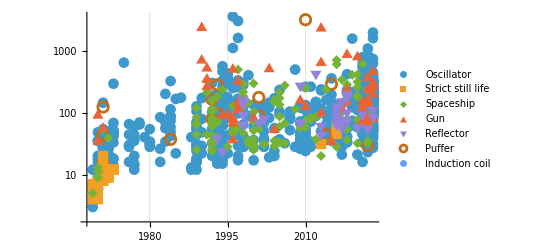

```mathematica
With[{sortedData=ReverseSortBy[$LifeNames,Length]},ListLogPlot[KeyValueMap[Legended[{#Year,#InitialWeight}&/@Lookup[$LifeData,#2],#1]&,sortedData],PlotMarkers->Automatic,GridLines->{Range[1968,2024]+.5,None}]]
```

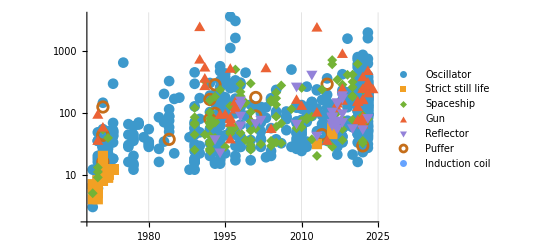

```mathematica
With[{sortedData=ReverseSortBy[$LifeNames,Length]},ListLogPlot[KeyValueMap[Legended[{#Year,#InitialWeight}&/@DeleteMissing[Lookup[lifeData,#2]],#1]&,sortedData],PlotMarkers->Automatic,GridLines->{Range[1968,2024]+.5,None}]]
```

The new data is very similar, note that I’m deleting the missing ones and using the old categories from $LifeNames because I haven’t been able yet to find how exactly $LifeNames was created so I’m having trouble reproducing it. There are no reflectors in the newLifeNames.

#### Adding callout

```mathematica
SeedRandom[3333];
With[{sortedData=ReverseSortBy[$LifeNames,Length]},
tocallout = RandomSample[Catenate[KeyValueMap[Function[{key, values}, {#Year, #InitialWeight}&/@DeleteMissing[Lookup[lifeData, values]]][#1, #2]&,ReverseSortBy[newLifeNames,Length]]], 10];ListLogPlot[KeyValueMap[Legended[With[{xy = {#Year,#InitialWeight}}, If[MemberQ[tocallout, xy], Callout[xy,ArrayPlot[#MatrixData, ImageSize->Tiny],Above, LabelVisibility->All], xy]]&/@DeleteMissing[Lookup[lifeData, #2]],#1]&,sortedData],PlotMarkers->Automatic,GridLines->{Range[1968,2024]+.5,None}, PlotHighlighting->None]]
```

-Graphics-

Callout has potential but is kinda ugly right now

#### Histograms

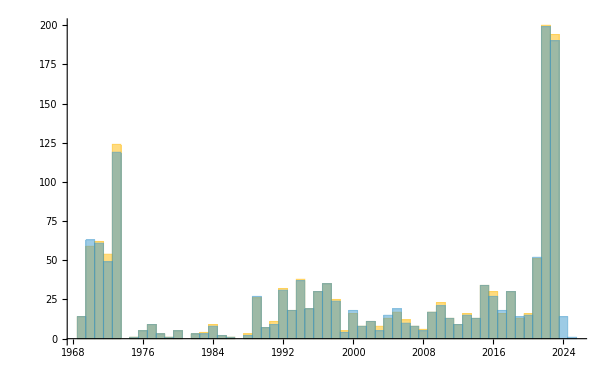

```mathematica
Histogram[{Values[#Year&/@$LifeData],Values[#Year&/@lifeData]} ,{1}]
```

Minor differences, same story

## Styling Stuff

### colorfunction

```mathematica
{c1,c2,c3,c4}=RGBColor/@{Hue[1, 0, 1],Hue[0.1, 0.74, 1],Hue[1, 0.84, 0.92],Hue[0.85, 1, 0.65]};
cf:=Blend[{{0,RGBColor@c1},{.2,c2},{.4,c3},{.9,c4}},#]&
cf2:=Blend[{{0,c1},{.2,Lighter[c2]},{.4,c3},{.9,c4}},#]&
```

### Trying with no gray

Original:

```mathematica
Image3D[CellularAutomaton["GameOfLife",{SparseArray[{{1,4},{2,5},{3,1},{3,5},{4,2},{4,3},{4,4},{4,5},{8,1},{9,2},{9,3},{10,3},{11,3},{12,2},{15,1},{15,4},{16,5},{17,1},{17,5},{18,2},{18,3},{18,4},{18,5}}->1],0},300],ColorFunction->(Blend[{{0.,Hue[0, 0, 0, 0.002]}, {1., RGBColor[1., 0.6436, 0.03622, 1.]}}, #1] & )]
```

-Graphics3D-

```mathematica
Image3D[CellularAutomaton["GameOfLife",{SparseArray[{{1,4},{2,5},{3,1},{3,5},{4,2},{4,3},{4,4},{4,5},{8,1},{9,2},{9,3},{10,3},{11,3},{12,2},{15,1},{15,4},{16,5},{17,1},{17,5},{18,2},{18,3},{18,4},{18,5}}->1],0},300],ColorFunction->(Blend[{{0.,Hue[0, 0, 0, 0]}, {1., RGBColor[1., 0.6436, 0.03622, 1.]}}, #1] & )]
```

-Graphics3D-

```mathematica
ArrayPlot3D[CellularAutomaton["GameOfLife",{SparseArray[{{1,4},{2,5},{3,1},{3,5},{4,2},{4,3},{4,4},{4,5},{8,1},{9,2},{9,3},{10,3},{11,3},{12,2},{15,1},{15,4},{16,5},{17,1},{17,5},{18,2},{18,3},{18,4},{18,5}}->1],0},300],ColorFunction->(Blend[{{0.,Hue[0, 0, 0, 0.002]}, {1., RGBColor[1., 0.6436, 0.03622, 1.]}}, #1] & ), Background->None, Boxed->True]
```

-Graphics3D-

I would say a little harder to see the depth

## Looking at Oscillator’s As a Case Study

```mathematica
os = Select[Values[lifeData], #Class === "Oscillator"&];
```

```mathematica
matrices=SortBy[RandomSample[os, 100],#Year&][[All,"MatrixData"]];
mds=Max/@Transpose[Dimensions/@matrices];
```

```mathematica
mds
```

{149,136}

```mathematica
padMatrix[m_, maxDims_]:=Module[{dims,padAmounts},dims=Dimensions[m];
padAmounts=Floor[(maxDims-dims)/2];ArrayPad[m,Transpose[{padAmounts,maxDims-dims-padAmounts}]]];
```

```mathematica
paddedMatrices=padMatrix[#, mds]&/@matrices;
```

```mathematica
ArrayPlot[padMatrix[#, {50, 50}],Mesh->False, ImageSize->{60, 60}]&/@paddedMatrices
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Pad each matrix to center it within maxDims*)
paddedMatrices=Map[Function[m,ArrayPad[m,Floor[(maxDims-Dimensions[m])/2]->"Fixed"]],matrices];
```

ArrayPad::mlens: Padding amount {5,4}→Fixed should be an integer, pair of integers, or list of pairs of integers.

ArrayPad::mlens: Padding amount {4,3}→Fixed should be an integer, pair of integers, or list of pairs of integers.

ArrayPad::mlens: Padding amount {3,3}→Fixed should be an integer, pair of integers, or list of pairs of integers.

General::stop: Further output of ArrayPad::mlens will be suppressed during this calculation.

```mathematica
(*Plot the padded matrices*)
ArrayPlot[#,Mesh->True]&/@paddedMatrices
```

{12,11}

ArrayPad::mlens: Padding amount {5,4}→Fixed should be an integer, pair of integers, or list of pairs of integers.

ArrayPad::mlens: Padding amount {4,3}→Fixed should be an integer, pair of integers, or list of pairs of integers.

ArrayPad::mlens: Padding amount {3,3}→Fixed should be an integer, pair of integers, or list of pairs of integers.

General::stop: Further output of ArrayPad::mlens will be suppressed during this calculation.

ArrayPlot::mat: Argument … at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{ArrayPlot[ArrayPad[SparseArray[…],{5,4}→Fixed],Mesh→True],ArrayPlot[ArrayPad[SparseArray[…],{4,3}→Fixed],Mesh→True],ArrayPlot[ArrayPad[SparseArray[…],{3,3}→Fixed],Mesh→True],ArrayPlot[ArrayPad[SparseArray[…],{1,1}→Fixed],Mesh→True],ArrayPlot[ArrayPad[SparseArray[…],{4,3}→Fixed],Mesh→True],ArrayPlot[ArrayPad[SparseArray[…],{3,2}→Fixed],Mesh→True],ArrayPlot[ArrayPad[SparseArray[…],{1,0}→Fixed],Mesh→True],ArrayPlot[ArrayPad[SparseArray[…],{0,0}→Fixed],Mesh→True],ArrayPlot[ArrayPad[SparseArray[…],{1,1}→Fixed],Mesh→True],ArrayPlot[ArrayPad[SparseArray[…],{4,0}→Fixed],Mesh→True]}

### Zooming in on a single discovery history

Block on table (10)
Block on cap (12)
Block on cover (12)
Cis-block on long bookend (12)
Trans-block on long bookend (12)
Block on dock (14)
Eater 2 (19)
Mango with block on dock (

## Other

Looked through 2018 stuff, nothing new there

What was Nik doing? His was a few scraping functions for getting the patterns